```mathematica
(*Mathematica*)
```

```mathematica
Clear[f,g]
```

```mathematica
(*(Hoffman page 158ff H^Infinity Theorems)*)
```

```mathematica
(* Decrement 1+x Markov recursion*)
```

```mathematica
f[0]=(1-x)/(1-x)
```

1

```mathematica
f[1]=(2-x)*(1+x)/(1-x)
```

((2-x) (1+x))/(1-x)

```mathematica
f[n_]:=f[n]=(2-x)*f[n-1]
```

```mathematica
Table[f[n],{n,0,10}]
```

{1,((2-x) (1+x))/(1-x),((2-x)^2 (1+x))/(1-x),((2-x)^3 (1+x))/(1-x),((2-x)^4 (1+x))/(1-x),((2-x)^5 (1+x))/(1-x),((2-x)^6 (1+x))/(1-x),((2-x)^7 (1+x))/(1-x),((2-x)^8 (1+x))/(1-x),((2-x)^9 (1+x))/(1-x),((2-x)^10 (1+x))/(1-x)}

```mathematica
Together[Sum[f[n],{n,0,100}]]
```

1/(-1+x)(-2535301200456458802993406410751+122962108222138251945180210921476 x-2949822946731089817282828358909950 x^2+46662852419701238383794393341493250 x^3-547488945315395595314590076215754750 x^4+5081109085228421742588105465389907970 x^5-38847834164648037710698449393808310270 x^6+251621096712086102347767750083339091970 x^7-1409161910847018818819851492297573138430 x^8+6930239943349341362256869062392904941570 x^9-30296849933783210486069611493745389207550 x^10+118893532982907091996996359825930047193090 x^11-422191877522915345631804499924052242071550 x^12+1365660265581987464015806732466623503925250 x^13-4046545201640337367910635433613993550282750 x^14+11035467367019207830391050069197325974110210 x^15-27810637373969028650760988577846302932467710 x^16+64988390618391758498657770412313477233246210 x^17-141231671586854435166717249565819367579451390 x^18+286132273114807084600342824730969093710020610 x^19-541529233124077392015196852490477892987256830 x^20+958959143832811812189165895669492324392501250 x^21-1590821804422601311039226746308638884161912830 x^22+2474046373955593523092993407569541303388602370 x^23-3607858665663296474945745080240614659044933630 x^24+4931136009961625082300643756644844312211750914 x^25-6308224503254083634074944968828323906365423614 x^26+7532839832465261359239437443096966585030541314 x^27-8356137083539088760636766856307065866827071486 x^28+8537315384626455907047703232139750245780160514 x^29-7905645017721340902831847653948484103824211966 x^30+6415643074646095028353567633934816781315080194 x^31-4176142910333987795752312422728874498319187966 x^32+1440713293822116732182623970956416331789893634 x^33+1440713293822116732182623970956416331789893634 x^34-4095902107417472016781813331390513200746201086 x^35+6208354333778429266013111647977383429251530754 x^36-7577069824037708936644963662258045846015705086 x^37+8143150706805255680421262568712180520517107714 x^38-7980152401751631106313328437411128573362700286 x^39+7256369035834626907150860063375398520353718274 x^40-6183977110328860852693566378375318468818894846 x^41+4970595881725190213299767131104868420154294274 x^42-3784446873666070797799651611801092219446755326 x^43+2737617805223883743297137603242489570155036674 x^44-1885801378255884031391475195866182854029344766 x^45+1239118307020955057429682071515568072988557314 x^46-777673830285373716206667654241448482746400766 x^47+466661062123178491886272481041326155006738434 x^48-267968138205485712600084304366142836669677566 x^49+147342236380319117669536064984212966624722946 x^50-77617549853658498726508301747229760159743998 x^51+39188492998599109786822427132557809516806146 x^52-18969652027420139735014151712200152324243454 x^53+8805680392413614909917547736076067268460546 x^54-3920471916310214491032976374770491526742014 x^55+1674273613970584658874694514096575562645506 x^56-685870234130326625257010350505241415254014 x^57+269510334066444059473964632167158260957186 x^58-101576751038233819482275650650511104802814 x^59+36715036010776136742083228079540345503746 x^60-12724713835874963623119473206676030488574 x^61+4227745191590825868891488883101866655746 x^62-1346192583879785188572432892448689094654 x^63+410678967117147714776917451676890169346 x^64-119986337260900223721937600984630951934 x^65+33559048952102894357887516892016410626 x^66-8981044056536962050422240579405479934 x^67+2298526059390272603296255719835172866 x^68-562234477257939084241044066204123134 x^69+131353995709015096329223718656016386 x^70-29289343882705120766863342626144254 x^71+6228271364863650955957708085264386 x^72-1261925073430412294889557475721214 x^73+243381210079829106874619248246786 x^74-44634058831797081329593231605758 x^75+7774367828309481158143763283970 x^76-1284478956786241918740893532158 x^77+201020665098864727736912445442 x^78-29753154181330205835589058558 x^79+4157776485120660792147968002 x^80-547524415189349418947051518 x^81+67802946968472362680320002 x^82-7877376188488649618227198 x^83+856383165145092082892802 x^84-86862845047352020828158 x^85+8192954429405912104962 x^86-715900340299075420158 x^87+57703043433883402242 x^88-4268929669984501758 x^89+288201281491845122 x^90-17634429929840638 x^91+969992637573122 x^92-47490613703678 x^93+2044272312322 x^94-76168422398 x^95+2406652642 x^96-62700398 x^97+1293202 x^98-19798 x^99+200 x^100-x^101)

```mathematica
(* Inverse Increment 1+x Markov recursion*)
```

```mathematica
g[0]=(1-x)/(1+x)
```

(1-x)/(1+x)

```mathematica
g[1]=((1-x)/(1+x))/(2-x)
```

(1-x)/((2-x) (1+x))

```mathematica
g[n_]:=g[n]=(1/(2-x))*g[n-1]
```

```mathematica
Table[g[n],{n,0,10}]
```

{(1-x)/(1+x),(1-x)/((2-x) (1+x)),(1-x)/((2-x)^2 (1+x)),(1-x)/((2-x)^3 (1+x)),(1-x)/((2-x)^4 (1+x)),(1-x)/((2-x)^5 (1+x)),(1-x)/((2-x)^6 (1+x)),(1-x)/((2-x)^7 (1+x)),(1-x)/((2-x)^8 (1+x)),(1-x)/((2-x)^9 (1+x)),(1-x)/((2-x)^10 (1+x))}

```mathematica
Together[Sum[g[n],{n,0,100}]]
```

-1/((-2+x)^100 (1+x))(-1+x) (2535301200456458802993406410751-125497409422594710748173617332225 x+3075320356153684528031001976242175 x^2-49738172775854922911825395317735425 x^3+597227118091250518226415471533490175 x^4-5678336203319672260814520936923398145 x^5+44526170367967709971512970330731708415 x^6-296147267080053812319280720414070800385 x^7+1705309177927072631139132212711643938815 x^8-8635549121276413993396001275104548880385 x^9+38932399055059624479465612768849938087935 x^10-157825932037966716476461972594779985281025 x^11+580017809560882062108266472518832227352575 x^12-1945678075142869526124073204985455731277825 x^13+5992223276783206894034708638599449281560575 x^14-17027690643802414724425758707796775255670785 x^15+44838328017771443375186747285643078188138495 x^16-109826718636163201873844517697956555421384705 x^17+251058390223017637040561767263775923000836095 x^18-537190663337824721640904591994745016710856705 x^19+1078719896461902113656101444485222909698113535 x^20-2037679040294713925845267340154715234090614785 x^21+3628500844717315236884494086463354118252527615 x^22-6102547218672908759977487494032895421641129985 x^23+9710405884336205234923232574273510080686063615 x^24-14641541894297830317223876330918354392897814529 x^25+20949766397551913951298821299746678299263238143 x^26-28482606230017175310538258742843644884293779457 x^27+36838743313556264071175025599150710751120850943 x^28-45376058698182719978222728831290460996901011457 x^29+53281703715904060881054576485238945100725223423 x^30-59697346790550155909408144119173761882040303617 x^31+63873489700884143705160456541902636380359491583 x^32-65314202994706260437343080512859052712149385217 x^33+63873489700884143705160456541902636380359491583 x^34-59777587593466671688378643210512123179613290497 x^35+53569233259688242422365531562534739750361759743 x^36-45992163435650533485720567900276693904346054657 x^37+37849012728845277805299305331564513383828946943 x^38-29868860327093646698985976894153384810466246657 x^39+22612491291259019791835116830777986290112528383 x^40-16428514180930158939141550452402667821293633537 x^41+11457918299204968725841783321297799401139339263 x^42-7673471425538897928042131709496707181692583937 x^43+4935853620315014184744994106254217611537547263 x^44-3050052242059130153353518910388034757508202497 x^45+1810933935038175095923836838872466684519645183 x^46-1033260104752801379717169184631018201773244417 x^47+566599042629622887830896703589692046766505983 x^48-298630904424137175230812399223549210096828417 x^49+151288668043818057561276334239336243472105471 x^50-73671118190159558834768032492106483312361473 x^51+34482625191560449047945605359548673795555327 x^52-15512973164140309312931453647348521471311873 x^53+6707292771726694403013905911272454202851327 x^54-2786820855416479911980929536501962676109313 x^55+1112547241445895253106235022405387113463807 x^56-426677007315568627849224671900145698209793 x^57+157166673249124568375260039732987437252607 x^58-55589922210890748892984389082476332449793 x^59+18874886200114612150901161002935986946047 x^60-6150172364239648527781687796259956457473 x^61+1922427172648822658890198913158089801727 x^62-576234588769037470317766020709400707073 x^63+165555621651889755540848569032510537727 x^64-45569284390989531818910968047879585793 x^65+12010235438886637461023451155863175167 x^66-3029191382349675410601210576457695233 x^67+730665322959402807304954856622522367 x^68-168430845701463723063910790418399233 x^69+37076849992448626734687071762382847 x^70-7787506109743505967823729136238593 x^71+1559234744879855011866021050974207 x^72-297309671449442716976463575252993 x^73+53928461369613610101844327006207 x^74-9294402537816528772251095400449 x^75+1520034709507047614107332116479 x^76-235555752720805695366438584321 x^77+34535087621940967629526138879 x^78-4781933440610761793937080321 x^79+624156955490101001789112319 x^80-76632540300751582842060801 x^81+8829593332279220161740799 x^82-952217143790570543513601 x^83+95833978645478460620799 x^84-8971133598126439792641 x^85+778179168720527687679 x^86-62278828421452267521 x^87+4575784987568865279 x^88-306855317584363521 x^89+18654036092518399 x^90-1019606162677761 x^91+49613525104639 x^92-2122911400961 x^93+78639088639 x^94-2470666241 x^95+64013599 x^96-1313201 x^97+19999 x^98-201 x^99+x^100)

```mathematica
Sum[f[n]*g[n],{n,0,100}]/(101)
```

1/101 (100+(1-x)/(1+x))

```mathematica
Grid[Table[x/.NSolve[Expand[(-1+x)*Sum[f[n],{n,0,i}]],x],{i,10}]]
```

1.73205 | -1.73205 |  |  |  |  |  |  |  |  | 
3.39138 | 1.77287 | -1.16425 |  |  |  |  |  |  |  | 
2.63558-1.03952 ⅈ | 2.63558+1.03952 ⅈ | 1.77917 | -1.05033 |  |  |  |  |  |  | 
3.18366 | 2.0262-1.12911 ⅈ | 2.0262+1.12911 ⅈ | 1.78043 | -1.01648 |  |  |  |  |  | 
2.92893-0.658121 ⅈ | 2.92893+0.658121 ⅈ | 1.68346-1.03464 ⅈ | 1.68346+1.03464 ⅈ | 1.7807 | -1.00548 |  |  |  |  | 
3.12002 | 2.56671-0.947777 ⅈ | 2.56671+0.947777 ⅈ | 1.78076 | 1.48381-0.91982 ⅈ | 1.48381+0.91982 ⅈ | -1.00183 |  |  |  | 
2.99409-0.470584 ⅈ | 2.99409+0.470584 ⅈ | 2.25613-1.049 ⅈ | 2.25613+1.049 ⅈ | 1.78077 | 1.3597-0.817195 ⅈ | 1.3597+0.817195 ⅈ | -1.00061 |  |  | 
3.08914 | 2.77291-0.757945 ⅈ | 2.77291+0.757945 ⅈ | 2.01438-1.06208 ⅈ | 2.01438+1.06208 ⅈ | 1.78078 | 1.27785-0.73099 ⅈ | 1.27785+0.73099 ⅈ | -1.0002 |  | 
3.01437-0.364354 ⅈ | 3.01437+0.364354 ⅈ | 2.54425-0.919478 ⅈ | 2.54425+0.919478 ⅈ | 1.82986-1.03537 ⅈ | 1.82986+1.03537 ⅈ | 1.78078 | 1.22116-0.659357 ⅈ | 1.22116+0.659357 ⅈ | -1.00007 | 
3.0709 | 2.8678-0.621711 ⅈ | 2.8678+0.621711 ⅈ | 2.33758-1.00188 ⅈ | 2.33758+1.00188 ⅈ | 1.68849-0.991829 ⅈ | 1.68849+0.991829 ⅈ | 1.78078 | 1.1803-0.599573 ⅈ | 1.1803+0.599573 ⅈ | -1.00002

```mathematica
(*elliptical roots plot*)
```

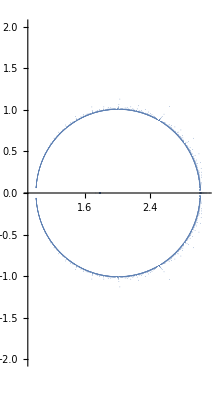

```mathematica
ga=Show[Table[ComplexListPlot[x/.NSolve[Expand[(-1+x)*Sum[f[n],{n,0,i}]],x],ImageSize->Full,PlotStyle->PointSize[0.001],PlotRange->{{0.9,3.1},{-2,2}}],{i,100}],PlotRange->{{0.9,3.1},{-2,2}}]
```

```mathematica
Export["Twin_Markov_Decrement3_roots2.jpg",ga]
```

Twin_Markov_Decrement3_roots2.jpg

```mathematica
(*end*)
```